```mathematica
ClearAll["Global`*"]
Clear[Derivative]
Needs["PlotLegends`"]
```

## Q2.1

```mathematica
PlotFiles =  FileNames["Q21*A.csv",NotebookDirectory[]];
ErrorPlotFiles =  FileNames["Q21*E.csv",NotebookDirectory[]];
Q2Plots=Import[#]&/@PlotFiles;
Q2ErrorPlots=Import[#]&/@ErrorPlotFiles;
p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];

(* (Log[Abs[Q2ErrorPlots[[1,-1,2]]]]-Log[Abs[Q2ErrorPlots[[1,1,2]]]])/(Q2ErrorPlots[[1,-1,1]]-Q2ErrorPlots[[1,1,1]]) *)

Show[ListLinePlot[Q2ErrorPlots,FrameLabel->{"x","F̂(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick]]
```

-Graphics-

```mathematica
y[x_]:=ⅇ^(-x)-ⅇ^(-4x);
rounded[num_,prec_]:=PaddedForm[num,{IntegerPart[Log[10,Abs[num]]]+prec,prec}];

For[i=0,i≤25,i++,
Print["$", PaddedForm[i*0.4,{2,1}],"$ & $",TeXForm[rounded[y[i*0.4],2]],
"$ & $",TeXForm[ScientificForm[Q2Plots[[1,i+1,2]],3]],"$ & $",TeXForm[ScientificForm[Q2ErrorPlots[[1,i+1,2]],3]],
"$ & $",TeXForm[ScientificForm[Q2Plots[[2,2 i+1,2]],3]],"$ & $",TeXForm[ScientificForm[Q2ErrorPlots[[2,2i+1,2]],3]],"$ \\\\ \hline"
]
]
```

$ 0.0$ & $\text{ 0.00}$ & $0.$ & $0.$ & $0.$ & $0.$ \\ \hline

$ 0.4$ & $\text{ 0.47}$ & $1.20$ & $7.32\times 10^{-1}$ & $2.25\times 10^{-2}$ & $-4.46\times 10^{-1}$ \\ \hline

$ 0.8$ & $\text{ 0.41}$ & $-2.23$ & $-2.64$ & $-1.51$ & $-1.92$ \\ \hline

$ 1.2$ & $\text{ 0.29}$ & $9.42$ & $9.13$ & $-7.98$ & $-8.27$ \\ \hline

$ 1.6$ & $\text{ 0.20}$ & $-3.16\times 10^1$ & $-3.18\times 10^1$ & $-3.56\times 10^1$ & $-3.58\times 10^1$ \\ \hline

$ 2.0$ & $\text{ 0.13}$ & $1.11\times 10^2$ & $1.11\times 10^2$ & $-1.55\times 10^2$ & $-1.55\times 10^2$ \\ \hline

$ 2.4$ & $\text{ 0.09}$ & $-3.87\times 10^2$ & $-3.87\times 10^2$ & $-6.71\times 10^2$ & $-6.71\times 10^2$ \\ \hline

$ 2.8$ & $\text{ 0.06}$ & $1.35\times 10^3$ & $1.35\times 10^3$ & $-2.90\times 10^3$ & $-2.90\times 10^3$ \\ \hline

$ 3.2$ & $\text{ 0.04}$ & $-4.71\times 10^3$ & $-4.71\times 10^3$ & $-1.26\times 10^4$ & $-1.26\times 10^4$ \\ \hline

$ 3.6$ & $\text{ 0.03}$ & $1.64\times 10^4$ & $1.64\times 10^4$ & $-5.44\times 10^4$ & $-5.44\times 10^4$ \\ \hline

$ 4.0$ & $\text{ 0.02}$ & $-5.72\times 10^4$ & $-5.72\times 10^4$ & $-2.36\times 10^5$ & $-2.36\times 10^5$ \\ \hline

$ 4.4$ & $\text{ 0.01}$ & $2.00\times 10^5$ & $2.00\times 10^5$ & $-1.02\times 10^6$ & $-1.02\times 10^6$ \\ \hline

$ 4.8$ & $\text{ 0.01}$ & $-6.96\times 10^5$ & $-6.96\times 10^5$ & $-4.42\times 10^6$ & $-4.42\times 10^6$ \\ \hline

$ 5.2$ & $\text{ 0.01}$ & $2.43\times 10^6$ & $2.43\times 10^6$ & $-1.91\times 10^7$ & $-1.91\times 10^7$ \\ \hline

$ 5.6$ & $\text{ 0.00}$ & $-8.46\times 10^6$ & $-8.46\times 10^6$ & $-8.28\times 10^7$ & $-8.28\times 10^7$ \\ \hline

$ 6.0$ & $\text{ 0.00}$ & $2.95\times 10^7$ & $2.95\times 10^7$ & $-3.58\times 10^8$ & $-3.58\times 10^8$ \\ \hline

$ 6.4$ & $\text{ 0.00}$ & $-1.03\times 10^8$ & $-1.03\times 10^8$ & $-1.55\times 10^9$ & $-1.55\times 10^9$ \\ \hline

$ 6.8$ & $\text{ 0.00}$ & $3.59\times 10^8$ & $3.59\times 10^8$ & $-6.71\times 10^9$ & $-6.71\times 10^9$ \\ \hline

$ 7.2$ & $\text{ 0.00}$ & $-1.25\times 10^9$ & $-1.25\times 10^9$ & $-2.91\times 10^{10}$ & $-2.91\times 10^{10}$ \\ \hline

$ 7.6$ & $\text{ 0.00}$ & $4.36\times 10^9$ & $4.36\times 10^9$ & $-1.26\times 10^{11}$ & $-1.26\times 10^{11}$ \\ \hline

$ 8.0$ & $\text{ 0.00}$ & $-1.52\times 10^{10}$ & $-1.52\times 10^{10}$ & $-5.45\times 10^{11}$ & $-5.45\times 10^{11}$ \\ \hline

$ 8.4$ & $\text{ 0.00}$ & $5.30\times 10^{10}$ & $5.30\times 10^{10}$ & $-2.36\times 10^{12}$ & $-2.36\times 10^{12}$ \\ \hline

$ 8.8$ & $\text{ 0.00}$ & $-1.85\times 10^{11}$ & $-1.85\times 10^{11}$ & $-1.02\times 10^{13}$ & $-1.02\times 10^{13}$ \\ \hline

$ 9.2$ & $\text{ 0.00}$ & $6.44\times 10^{11}$ & $6.44\times 10^{11}$ & $-4.42\times 10^{13}$ & $-4.42\times 10^{13}$ \\ \hline

$ 9.6$ & $\text{ 0.00}$ & $-2.25\times 10^{12}$ & $-2.25\times 10^{12}$ & $-1.91\times 10^{14}$ & $-1.91\times 10^{14}$ \\ \hline

$ 10.0$ & $\text{ 0.00}$ & $7.83\times 10^{12}$ & $7.83\times 10^{12}$ & $-8.28\times 10^{14}$ & $-8.28\times 10^{14}$ \\ \hline

```mathematica
For[i=0,i≤5,i++,
Print["$", PaddedForm[i*2,{2,1}],"$ & $",TeXForm[rounded[N[y[i*2]],2]],
"$ & $",TeXForm[rounded[Q2Plots[[3,20i+1,2]],2]],"$ & $",TeXForm[rounded[Q2ErrorPlots[[3,20i+1,2]],2]],
"$ & $",TeXForm[rounded[Q2Plots[[4,40i+1,2]],2]],"$ & $",TeXForm[rounded[Q2ErrorPlots[[4,40i+1,2]],2]],"$ \\\\ \hline"
]
]
```

$  0$ & $\text{ 0.00}$ & $\text{ 0.00}$ & $\text{ 0.00}$ & $\text{ 0.00}$ & $\text{ 0.00}$ \\ \hline

$  2$ & $\text{ 0.13}$ & $-81.60$ & $-81.70$ & $-25.60$ & $-25.70$ \\ \hline

$  4$ & $\text{ 0.02}$ & $-199570.40$ & $-199570.40$ & $-72802.20$ & $-72802.20$ \\ \hline

$  6$ & $\text{ 0.00}$ & $\text{       -4.87}\times 10^8$ & $\text{       -4.87}\times 10^8$ & $\text{       -2.06}\times 10^8$ & $\text{       -2.06}\times 10^8$ \\ \hline

$  8$ & $\text{ 0.00}$ & $\text{           -1.19}\times 10^{12}$ & $\text{           -1.19}\times 10^{12}$ & $\text{          -5.83}\times 10^{11}$ & $\text{          -5.83}\times 10^{11}$ \\ \hline

$ 10$ & $\text{ 0.00}$ & $\text{              -2.91}\times 10^{15}$ & $\text{              -2.91}\times 10^{15}$ & $\text{              -1.65}\times 10^{15}$ & $\text{              -1.65}\times 10^{15}$ \\ \hline

## Q2.2

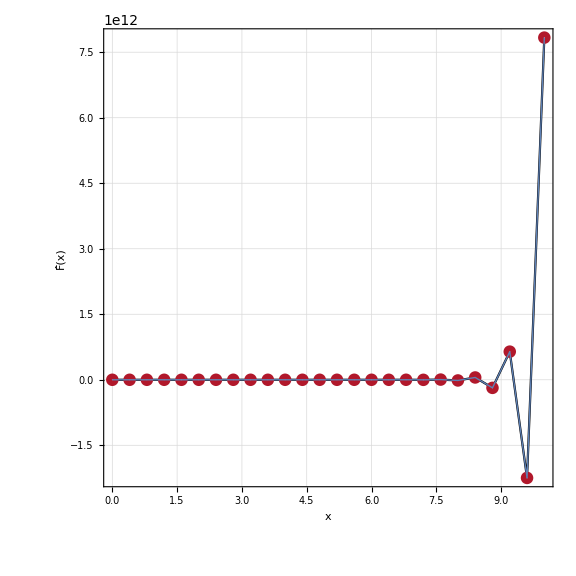

```mathematica
h=0.4;
A = 1/(2 Sqrt[16 h^2 + 1])(3h - 3/(4 - Sinh[h]/h)(ⅇ^(-h)+4h+Sqrt[16 h^2 + 1]));
B= 1/(2 Sqrt[16 h^2 + 1])(-3h + 3/(4 - Sinh[h]/h)(ⅇ^(-h)+4h-Sqrt[16 h^2 + 1]));
Y[n_]:=A(-4h+ Sqrt[16 h^2 + 1])^n + B (-4h -  Sqrt[16 h^2 + 1])^n +  3/(4 - Sinh[h]/h)ⅇ^(-n h)
Show[ListLinePlot[Q2Plots[[1]],FrameLabel->{"x","F̂(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Table[{n h,Y[n]},{n,0,25}],PlotRange->All,PlotStyle->Thick]]
```

```mathematica
h=0.05;
Log[(4h +Sqrt[16 h^2 + 1])] /h
```

3.9738

```mathematica
NumberForm[3.9738022069848284,16]
```

3.973802206984828

```mathematica
f
```

```mathematica
Y[1]
```

8.23664

## Q2.3

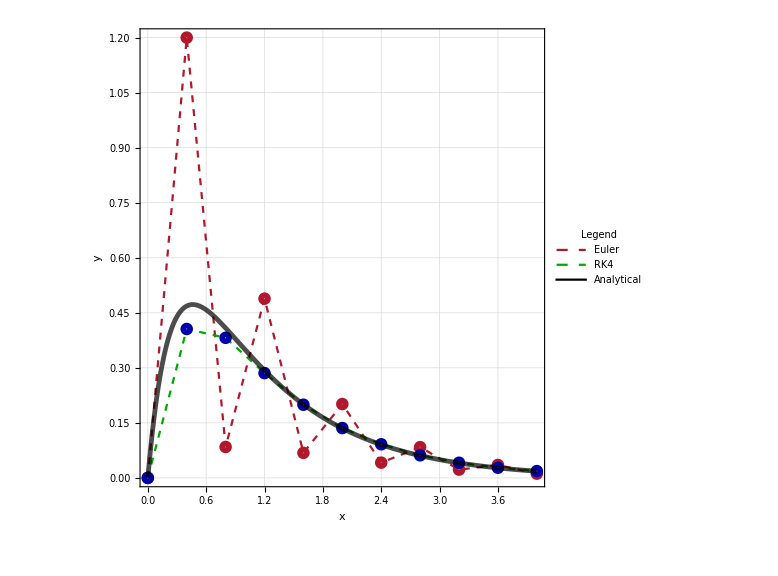

```mathematica
Q23Euler = Import[ FileNameJoin[{NotebookDirectory[], "Q2.3Euler.csv"}]];
Q23RK4= Import[ FileNameJoin[{NotebookDirectory[], "Q2.3RK4.csv"}]];

y[x_]:=ⅇ^(-x)-ⅇ^(-4x)

p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];

p=Graphics[{EdgeForm[{Darker[Green],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];

plot=Show[ListLinePlot[Q23Euler,FrameLabel->{"x","y"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{RGBColor[0.694118, 0.0941176, 0.168627],Dashed},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q23RK4,FrameLabel->{"x","y(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{Darker[Green],Dashed},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],Plot[y[x],{x,0,4},PlotStyle->{GrayLevel[0],Thickness[0.006],Opacity[0.7]},PlotRange->All]];

plotlegended=Legended[plot,LineLegend[{{RGBColor[0.694118, 0.0941176, 0.168627],Dashed},{Darker[Green],Dashed},GrayLevel[0]},{"Euler","RK4","Analytical"},LegendLabel->Style["Legend",FontFamily->"Times New Roman",20,Black],LabelStyle->{FontFamily->"Times New Roman",FontSize->20}]]
Export[FileNameJoin[{NotebookDirectory[],"Q23.eps"}],plotlegended];
```

```mathematica
rounded[num_,prec_]:=PaddedForm[num,{IntegerPart[Log[10,Abs[num]]]+prec,prec}];
```

```mathematica
Q23Euler[[
```

{{0.,0.},{0.400000000000000022,1.20000000000000018},{0.800000000000000044,0.0843840552427670421},{1.20000000000000018,0.488564323795005695},{1.60000000000000009,0.0682944600176390027},{2.,0.201299145583003075},{2.39999999999999991,0.0416228525341333921},{2.79999999999999982,0.0838878324268149817},{3.19999999999999973,0.0226393756941725699},{3.59999999999999965,0.0353310193575359297},{3.99999999999999956,0.0115898553222295239}}

```mathematica
For[i=0,i≤10,i++,
Print["$", PaddedForm[i*0.4,{2,1}],
"$ & $",TeXForm[rounded[Q23Euler[[i+1,2]],3]],"$ & $",TeXForm[rounded[Q23RK4[[i+1,2]],3]],"$ \\\\ \hline"
]
]
```

$ 0.0$ & $\text{ 0.000}$ & $\text{ 0.000}$ \\ \hline

$ 0.4$ & $\text{ 1.200}$ & $\text{ 0.406}$ \\ \hline

$ 0.8$ & $\text{ 0.084}$ & $\text{ 0.382}$ \\ \hline

$ 1.2$ & $\text{ 0.489}$ & $\text{ 0.286}$ \\ \hline

$ 1.6$ & $\text{ 0.068}$ & $\text{ 0.199}$ \\ \hline

$ 2.0$ & $\text{ 0.201}$ & $\text{ 0.136}$ \\ \hline

$ 2.4$ & $\text{ 0.042}$ & $\text{ 0.092}$ \\ \hline

$ 2.8$ & $\text{ 0.084}$ & $\text{ 0.062}$ \\ \hline

$ 3.2$ & $\text{ 0.023}$ & $\text{ 0.041}$ \\ \hline

$ 3.6$ & $\text{ 0.035}$ & $\text{ 0.028}$ \\ \hline

$ 4.0$ & $\text{ 0.012}$ & $\text{ 0.019}$ \\ \hline

## Q2.4

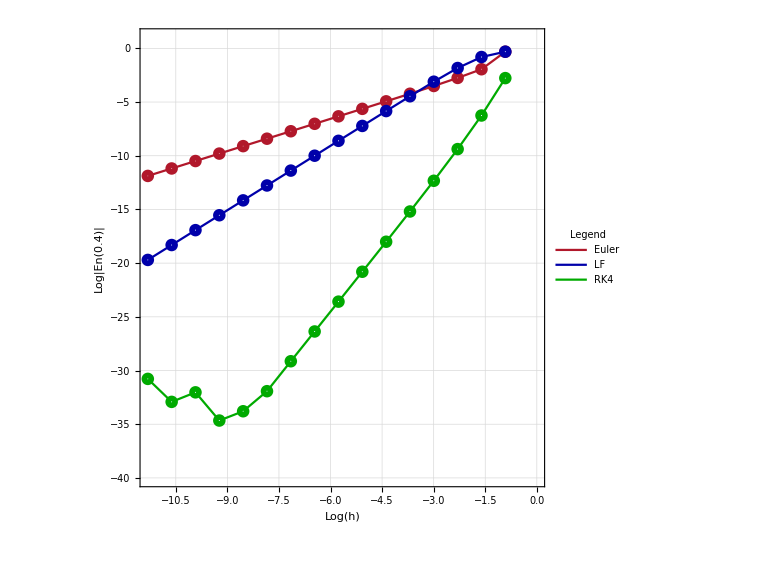

```mathematica
Q24Euler = Import[ FileNameJoin[{NotebookDirectory[], "Q2.4Euler.csv"}]];
Q24LF= Import[ FileNameJoin[{NotebookDirectory[], "Q2.4LF.csv"}]];
Q24RK4= Import[ FileNameJoin[{NotebookDirectory[], "Q2.4RK4.csv"}]];

Q24LogEuler = Import[ FileNameJoin[{NotebookDirectory[], "Q2.4LogEuler.csv"}]];
Q24LogLF= Import[ FileNameJoin[{NotebookDirectory[], "Q2.4logLF.csv"}]];
Q24LogRK4= Import[ FileNameJoin[{NotebookDirectory[], "Q2.4LogRK4.csv"}]];

y[x_]:=ⅇ^(-x)-ⅇ^(-4x)

p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p2=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p3=Graphics[{EdgeForm[{Darker[Green],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];

plot =Show[ListLinePlot[Q24LogEuler,FrameLabel->{"Log(h)","Log|En(0.4)|"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->{-40,1},GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{RGBColor[0.694118, 0.0941176, 0.168627]},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],
ListLinePlot[Q24LogLF,LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p2,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{Darker[Blue]},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],
ListLinePlot[Q24LogRK4,LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p3,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{Darker[Green]},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick]];
plotlegended=Legended[plot,LineLegend[{RGBColor[0.694118, 0.0941176, 0.168627],Darker[Blue],Darker[Green]},{"Euler","LF","RK4"},LegendLabel->Style["Legend",FontFamily->"Times New Roman",20,Black],LabelStyle->{FontFamily->"Times New Roman",FontSize->20}]]
Export[FileNameJoin[{NotebookDirectory[],"Q24.eps"}],plotlegended];
```

```mathematica
For[i=0,i≤15,i++,
Print["$", i,
"$ & $",TeXForm[ScientificForm[Q24Euler[[i+1,2]],3]],"$ & $",TeXForm[ScientificForm[Q24LF[[i+1,2]],3]],"$ & $",TeXForm[ScientificForm[Q24RK4[[i+1,2]],3]],"$ \\\\ \hline"
]
]
```

$0$ & $7.32\times 10^{-1}$ & $7.32\times 10^{-1}$ & $-6.26\times 10^{-2}$ \\ \hline

$1$ & $1.43\times 10^{-1}$ & $-4.46\times 10^{-1}$ & $-1.92\times 10^{-3}$ \\ \hline

$2$ & $6.37\times 10^{-2}$ & $-1.60\times 10^{-1}$ & $-8.42\times 10^{-5}$ \\ \hline

$3$ & $3.00\times 10^{-2}$ & $-4.48\times 10^{-2}$ & $-4.41\times 10^{-6}$ \\ \hline

$4$ & $1.46\times 10^{-2}$ & $-1.15\times 10^{-2}$ & $-2.53\times 10^{-7}$ \\ \hline

$5$ & $7.20\times 10^{-3}$ & $-2.91\times 10^{-3}$ & $-1.51\times 10^{-8}$ \\ \hline

$6$ & $3.57\times 10^{-3}$ & $-7.28\times 10^{-4}$ & $-9.24\times 10^{-10}$ \\ \hline

$7$ & $1.78\times 10^{-3}$ & $-1.82\times 10^{-4}$ & $-5.71\times 10^{-11}$ \\ \hline

$8$ & $8.89\times 10^{-4}$ & $-4.55\times 10^{-5}$ & $-3.55\times 10^{-12}$ \\ \hline

$9$ & $4.44\times 10^{-4}$ & $-1.14\times 10^{-5}$ & $-2.22\times 10^{-13}$ \\ \hline

$10$ & $2.22\times 10^{-4}$ & $-2.85\times 10^{-6}$ & $-1.37\times 10^{-14}$ \\ \hline

$11$ & $1.11\times 10^{-4}$ & $-7.12\times 10^{-7}$ & $2.11\times 10^{-15}$ \\ \hline

$12$ & $5.55\times 10^{-5}$ & $-1.78\times 10^{-7}$ & $-8.88\times 10^{-16}$ \\ \hline

$13$ & $2.77\times 10^{-5}$ & $-4.45\times 10^{-8}$ & $-1.23\times 10^{-14}$ \\ \hline

$14$ & $1.39\times 10^{-5}$ & $-1.11\times 10^{-8}$ & $5.05\times 10^{-15}$ \\ \hline

$15$ & $6.93\times 10^{-6}$ & $-2.78\times 10^{-9}$ & $4.30\times 10^{-14}$ \\ \hline

## Q3.6

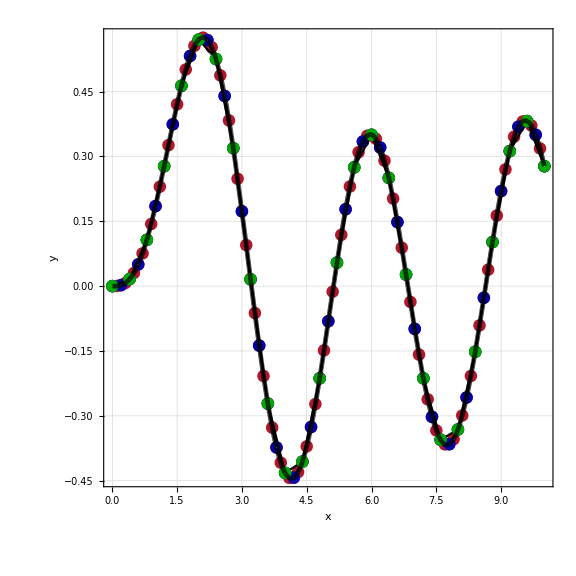

```mathematica
delta = 0;
Omega = 1;
a = 1;
gamma = 1;
omega = Sqrt[3];
k = Sqrt[4 Omega^2 - gamma^2];
A = (Omega^2-omega^2)/((Omega^2-omega^2)^2+gamma^2 omega^2)*a;
B = (- gamma * omega)/((Omega^2-omega^2)^2+gamma^2 omega^2)*a;
d= -B;
c = (gamma *d -2* omega*A)/k;
g[t_]:=A*Sin[omega t]+B Cos[omega t] + ⅇ^(-gamma t/2) (c Sin[k t/2]+d Cos[k t/2])

PlotFiles =  FileNames["Q3.6*.csv",NotebookDirectory[]];
ErrorPlotFiles =  FileNames["Q3.6Error*.csv",NotebookDirectory[]];
Q36Plots=Import[#]&/@PlotFiles;
Q36ErrorPlots=Import[#]&/@ErrorPlotFiles;

p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p2=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p3=Graphics[{EdgeForm[{Darker[Green],Thickness[0.3]}],FaceForm[LightGreen],Disk[]}];



Show[ListLinePlot[Q36Plots[[3]],FrameLabel->{"x","y"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q36Plots[[2]],LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p2,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q36Plots[[1]],LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p3,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],
Plot[g[x],{x,0,10},PlotStyle->{GrayLevel[0],Thickness[0.006],Opacity[0.7]},PlotRange->All]
]
```

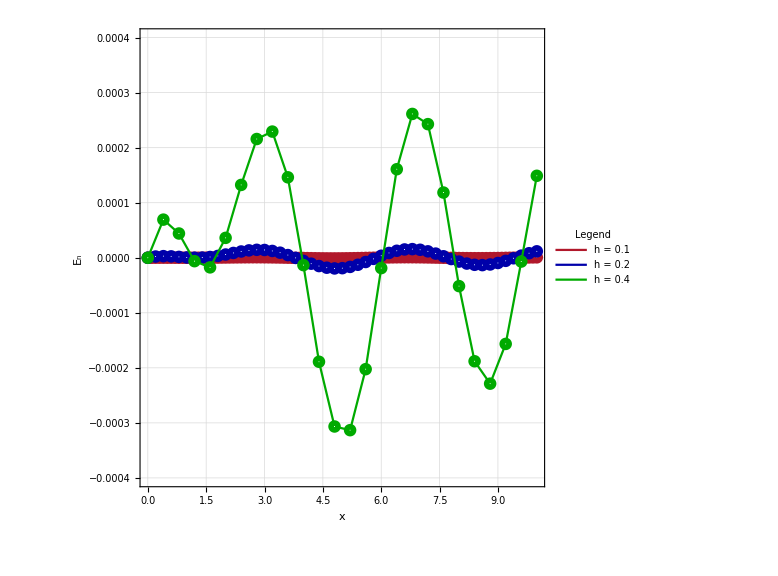

```mathematica
plot = Show[ListLinePlot[Q36ErrorPlots[[3]],FrameLabel->{"x","E_n"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->{-0.0004,0.0004},GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q36ErrorPlots[[2]],LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p2,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->Darker[Blue],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q36ErrorPlots[[1]],LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p3,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle-> {Darker[Green]},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick]
];
plotlegended=Legended[plot,LineLegend[{RGBColor[0.694118, 0.0941176, 0.168627],Darker[Blue],Darker[Green]},{"h = 0.1","h = 0.2","h = 0.4"},LegendLabel->Style["Legend",FontFamily->"Times New Roman",20,Black],LabelStyle->{FontFamily->"Times New Roman",FontSize->20}]]
Export[FileNameJoin[{NotebookDirectory[],"Q36.eps"}],plotlegended];
```

```mathematica
rounded[num_,prec_]:=PaddedForm[num,{IntegerPart[Log[10,Abs[num]]]+prec,prec}];

For[i=0,i≤25,i++,
Print["$", PaddedForm[i*0.4,{2,1}],"$ & $",TeXForm[PaddedForm[g[i*0.4],{3,2}]],
"$ & $",TeXForm[PaddedForm[Q36Plots[[1,i+1,2]],{3,2}]],"$ & $",TeXForm[ScientificForm[Q36ErrorPlots[[1,i+1,2]],3]],
"$ & $",TeXForm[rounded[Q36Plots[[2,2 i+1,2]],2]],"$ & $",TeXForm[ScientificForm[Q36ErrorPlots[[2,2i+1,2]],3]],
"$ & $",TeXForm[rounded[Q36Plots[[3,4 i+1,2]],2]],"$ & $",TeXForm[ScientificForm[Q36ErrorPlots[[3,4i+1,2]],3]],"$ \\\\ \hline"
]
]
```

$ 0.0$ & $\text{ 0.00}$ & $\text{ 0.00}$ & $0.$ & $\text{ 0.00}$ & $0.$ & $\text{ 0.00}$ & $0.$ \\ \hline

$ 0.4$ & $\text{ 0.02}$ & $\text{ 0.02}$ & $6.93\times 10^{-5}$ & $\text{ 0.02}$ & $2.94\times 10^{-6}$ & $\text{ 0.02}$ & $1.50\times 10^{-7}$ \\ \hline

$ 0.8$ & $\text{ 0.11}$ & $\text{ 0.11}$ & $4.41\times 10^{-5}$ & $\text{ 0.11}$ & $1.58\times 10^{-6}$ & $\text{ 0.11}$ & $7.95\times 10^{-8}$ \\ \hline

$ 1.2$ & $\text{ 0.28}$ & $\text{ 0.28}$ & $-6.19\times 10^{-6}$ & $\text{ 0.28}$ & $6.75\times 10^{-8}$ & $\text{ 0.28}$ & $3.69\times 10^{-8}$ \\ \hline

$ 1.6$ & $\text{ 0.46}$ & $\text{ 0.46}$ & $-1.75\times 10^{-5}$ & $\text{ 0.46}$ & $1.39\times 10^{-6}$ & $\text{ 0.46}$ & $1.74\times 10^{-7}$ \\ \hline

$ 2.0$ & $\text{ 0.57}$ & $\text{ 0.57}$ & $3.62\times 10^{-5}$ & $\text{ 0.57}$ & $5.91\times 10^{-6}$ & $\text{ 0.57}$ & $4.78\times 10^{-7}$ \\ \hline

$ 2.4$ & $\text{ 0.53}$ & $\text{ 0.53}$ & $1.32\times 10^{-4}$ & $\text{ 0.53}$ & $1.14\times 10^{-5}$ & $\text{ 0.53}$ & $7.90\times 10^{-7}$ \\ \hline

$ 2.8$ & $\text{ 0.32}$ & $\text{ 0.32}$ & $2.16\times 10^{-4}$ & $\text{ 0.32}$ & $1.44\times 10^{-5}$ & $\text{ 0.32}$ & $9.06\times 10^{-7}$ \\ \hline

$ 3.2$ & $\text{ 0.02}$ & $\text{ 0.02}$ & $2.29\times 10^{-4}$ & $\text{ 0.02}$ & $1.24\times 10^{-5}$ & $\text{ 0.02}$ & $6.92\times 10^{-7}$ \\ \hline

$ 3.6$ & $-0.27$ & $-0.27$ & $1.46\times 10^{-4}$ & $-0.27$ & $4.90\times 10^{-6}$ & $-0.27$ & $1.67\times 10^{-7}$ \\ \hline

$ 4.0$ & $-0.43$ & $-0.43$ & $-1.34\times 10^{-5}$ & $-0.43$ & $-5.64\times 10^{-6}$ & $-0.43$ & $-4.91\times 10^{-7}$ \\ \hline

$ 4.4$ & $-0.41$ & $-0.41$ & $-1.89\times 10^{-4}$ & $-0.41$ & $-1.51\times 10^{-5}$ & $-0.41$ & $-1.02\times 10^{-6}$ \\ \hline

$ 4.8$ & $-0.21$ & $-0.21$ & $-3.07\times 10^{-4}$ & $-0.21$ & $-1.94\times 10^{-5}$ & $-0.21$ & $-1.19\times 10^{-6}$ \\ \hline

$ 5.2$ & $\text{ 0.05}$ & $\text{ 0.05}$ & $-3.13\times 10^{-4}$ & $\text{ 0.05}$ & $-1.66\times 10^{-5}$ & $\text{ 0.05}$ & $-9.28\times 10^{-7}$ \\ \hline

$ 5.6$ & $\text{ 0.27}$ & $\text{ 0.27}$ & $-2.02\times 10^{-4}$ & $\text{ 0.27}$ & $-7.70\times 10^{-6}$ & $\text{ 0.27}$ & $-3.27\times 10^{-7}$ \\ \hline

$ 6.0$ & $\text{ 0.35}$ & $\text{ 0.35}$ & $-1.88\times 10^{-5}$ & $\text{ 0.35}$ & $3.65\times 10^{-6}$ & $\text{ 0.35}$ & $3.61\times 10^{-7}$ \\ \hline

$ 6.4$ & $\text{ 0.25}$ & $\text{ 0.25}$ & $1.61\times 10^{-4}$ & $\text{ 0.25}$ & $1.27\times 10^{-5}$ & $\text{ 0.25}$ & $8.48\times 10^{-7}$ \\ \hline

$ 6.8$ & $\text{ 0.03}$ & $\text{ 0.03}$ & $2.61\times 10^{-4}$ & $\text{ 0.03}$ & $1.57\times 10^{-5}$ & $\text{ 0.03}$ & $9.38\times 10^{-7}$ \\ \hline

$ 7.2$ & $-0.21$ & $-0.21$ & $2.43\times 10^{-4}$ & $-0.21$ & $1.17\times 10^{-5}$ & $-0.21$ & $6.10\times 10^{-7}$ \\ \hline

$ 7.6$ & $-0.36$ & $-0.36$ & $1.18\times 10^{-4}$ & $-0.36$ & $2.71\times 10^{-6}$ & $-0.36$ & $3.02\times 10^{-8}$ \\ \hline

$ 8.0$ & $-0.33$ & $-0.33$ & $-5.15\times 10^{-5}$ & $-0.33$ & $-6.94\times 10^{-6}$ & $-0.33$ & $-5.27\times 10^{-7}$ \\ \hline

$ 8.4$ & $-0.15$ & $-0.15$ & $-1.88\times 10^{-4}$ & $-0.15$ & $-1.28\times 10^{-5}$ & $-0.15$ & $-8.05\times 10^{-7}$ \\ \hline

$ 8.8$ & $\text{ 0.10}$ & $\text{ 0.10}$ & $-2.29\times 10^{-4}$ & $\text{ 0.10}$ & $-1.22\times 10^{-5}$ & $\text{ 0.10}$ & $-6.80\times 10^{-7}$ \\ \hline

$ 9.2$ & $\text{ 0.31}$ & $\text{ 0.31}$ & $-1.57\times 10^{-4}$ & $\text{ 0.31}$ & $-5.60\times 10^{-6}$ & $\text{ 0.31}$ & $-2.18\times 10^{-7}$ \\ \hline

$ 9.6$ & $\text{ 0.38}$ & $\text{ 0.38}$ & $-6.89\times 10^{-6}$ & $\text{ 0.38}$ & $3.87\times 10^{-6}$ & $\text{ 0.38}$ & $3.61\times 10^{-7}$ \\ \hline

$ 10.0$ & $\text{ 0.28}$ & $\text{ 0.28}$ & $1.49\times 10^{-4}$ & $\text{ 0.28}$ & $1.17\times 10^{-5}$ & $\text{ 0.28}$ & $7.80\times 10^{-7}$ \\ \hline

```mathematica
Q36ErrorPlots[[1]]
```

{{0.,0.},{0.400000000000000022,0.0000692874126720748051},{0.800000000000000044,0.0000440853834808713208},{1.20000000000000018,-6.18686572290139125×10^-6},{1.60000000000000009,-0.0000174665939643436907},{2.,0.0000361604044154528737},{2.40000000000000036,0.000132370458332586871},{2.80000000000000027,0.000215746258683424674},{3.20000000000000018,0.000229265347967581162},{3.60000000000000009,0.000146168323902406971},{4.,-0.0000133860544301867002},{4.40000000000000036,-0.000188943208563663312},{4.80000000000000071,-0.000306575937986081071},{5.20000000000000018,-0.000313246767074747134},{5.60000000000000053,-0.00020243694452382055},{6.,-0.000018775531686054947},{6.40000000000000036,0.000160855668997317292},{6.80000000000000071,0.000261314223599849044},{7.20000000000000018,0.000242779284815641816},{7.60000000000000053,0.00011849651692819041},{8.,-0.0000515250264221944754},{8.40000000000000036,-0.000188042433756863137},{8.80000000000000071,-0.00022875248498493983},{9.20000000000000107,-0.000156543167714962017},{9.60000000000000142,-6.89447498053441521×10^-6},{10.,0.000148911446705701778}}

## Q3.7

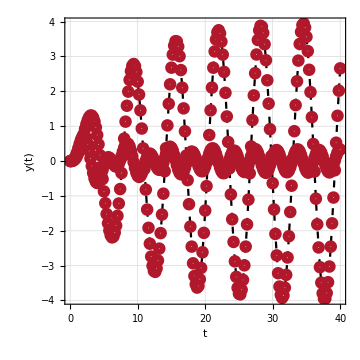
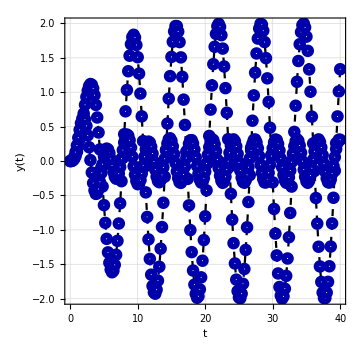
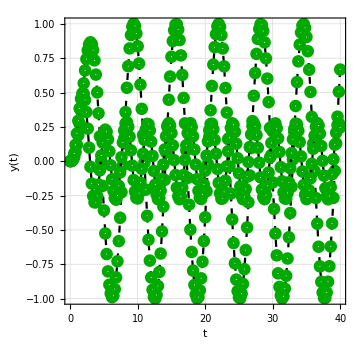
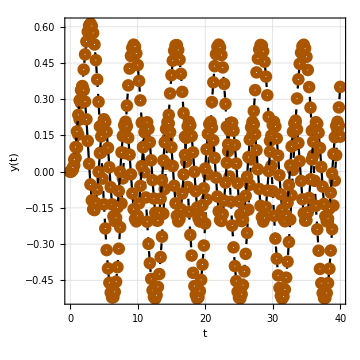

```mathematica
delta = 0;
Omega = 1;
a = 1;
gammaList = {0.25,0.5,1.0,1.9};
k = Sqrt[4 Omega^2 - gamma^2];
A = (Omega^2-omega^2)/((Omega^2-omega^2)^2+gamma^2 omega^2)*a;
B = (- gamma * omega)/((Omega^2-omega^2)^2+gamma^2 omega^2)*a;
d= -B;
c = (gamma *d/2 - omega*A)/(k/2);
g[t_,gamma_,omega_]:=A*Sin[omega t]+B Cos[Omega t] + ⅇ^(-gamma t/2) (c Sin[k t/2]+d Cos[k t/2])

PlotFiles =  FileNames["Q3.7*.csv",NotebookDirectory[]];
Q37Plots=Import[#]&/@PlotFiles;

p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p2=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p3=Graphics[{EdgeForm[{Darker[Green],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p4=Graphics[{EdgeForm[{Darker[Orange],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p={p1,p2,p3,p4};

Table[Show[ListLinePlot[Q37Plots[[i]],FrameLabel->{"t","y(t)"},LabelStyle->{FontSize->20, Black},ImageSize->Medium, Frame->True,PlotRange->All,GridLines->Automatic,PlotMarkers->{p[[i]],.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{GrayLevel[0],Dashed},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q37Plots[[i+4]],PlotMarkers->{p[[i]],.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick]],{i,1,4}]
```

## Q3.8

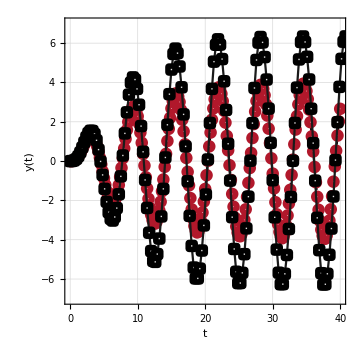
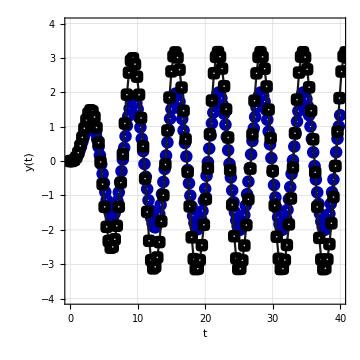
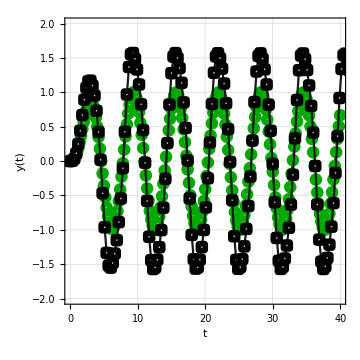
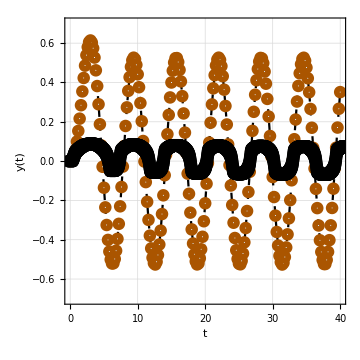

```mathematica
delta = 0;
Omega = 1;
a = 1;
gamma = 0;
deltaList = {0.25,0.5,1.0,20};

PlotFiles =  FileNames["Q3.8*.csv",NotebookDirectory[]];
Q38Plots=Import[#]&/@PlotFiles;

p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p2=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p3=Graphics[{EdgeForm[{Darker[Green],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p4=Graphics[{EdgeForm[{Darker[Orange],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
p={p1,p2,p3,p4};

q1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Rectangle[]}];
q2=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Rectangle[]}];
q3=Graphics[{EdgeForm[{Darker[Green],Thickness[0.3]}],FaceForm[LightGreen],Rectangle[]}];
q4=Graphics[{EdgeForm[{Darker[Orange],Thickness[0.3]}],FaceForm[LightOrange],Rectangle[]}];
q={q1,q2,q3,q4};

Table[Show[ListLinePlot[Q37Plots[[i]],FrameLabel->{"t","y(t)"},LabelStyle->{FontSize->20, Black},ImageSize->Medium, Frame->True,PlotRange->{{-7,7},{-4,4},{-2,2},{-0.7,0.7}}[[i]],GridLines->Automatic,PlotMarkers->{p[[i]],.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{GrayLevel[0],Dashed},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q38Plots[[i]],FrameLabel->{"t","y(t)"},LabelStyle->{FontSize->20, Black},ImageSize->Medium, Frame->True,GridLines->Automatic,PlotMarkers->{Graphics[{EdgeForm[{Black,Thickness[0.3]}],FaceForm[LightGray],Rectangle[]}],.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->{GrayLevel[0.1]},PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick]


],{i,1,4}]
```

## Other Stuff

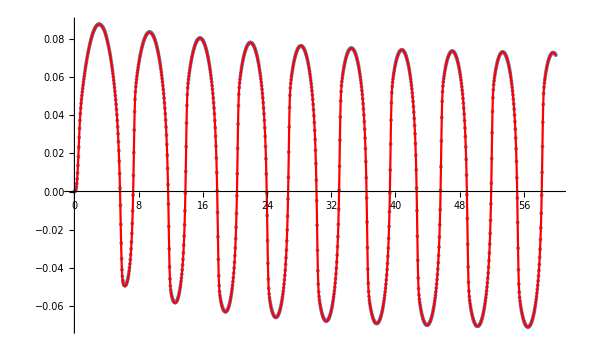

```mathematica
Q38Plots=Import[ FileNameJoin[{NotebookDirectory[], "3.8try60newnew.csv"}]];
delta = 20;
s=NDSolve[{y''[t] + delta^3 y[t]^2 y'[t] + y[t] == Sin[t],y'[0]==0,y[0]==0},y,{t,0,60}];
Y[t_]:=Evaluate[y[t]/.s];
Show[ListPlot[Q38Plots,PlotRange->All],Plot[Y[t],{t,0,60},PlotStyle->Red]]
```

```mathematica
DSolve[{y''[t]+1/2 Cos[t] (-B+(2B+c) Cos[2 t]+10 c Cos[4 t])+y[t]==0},y,{t,0,4Pi}]
```

{{y→Function[{t},((-43 omega-96 C[1]+96 omega^2 C[1]) Cos[t]+33 omega Cos[3 t]+10 omega Cos[5 t]-12 omega t Sin[t]-96 C[2] Sin[t]+96 omega^2 C[2] Sin[t])/(96 (-1+omega^2))]}}

```mathematica
FullSimplify[B(-2 Cos[t] Sin[t]^2 + Cos[t]^3)+c(-2 Cos[t]Sin[t]Sin[3t]+3 Cos[t]^2 Cos[3t])]
```

1/2 Cos[t] (-B+(3 B+c) Cos[2 t]+5 c Cos[4 t])